Take-up Calcs
We solve for takeup as a position of arm angles. We rename the variables to match the python variables. We then differentiate it for the statespace model.

```mathematica
LTakeupSide[a_,Larm_, dpdp_, dap_] := Sqrt[(Larm Cos[a] - dap)^2 + (Larm Sin[a])^2] + Sqrt[(dap + dpdp - Larm Cos[a])^2 + (Larm Sin[a])^2] - dpdp;
LTakeup[a_, b_, Larm_, dpdp_, dap_] := LTakeupSide[a,Larm, dpdp, dap] + LTakeupSide[b,Larm, dpdp, dap];
```

```mathematica
FullSimplify[LTakeup[Subscript[α, 1], Subscript[α, 2], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]]
```

-2 d_pdp+√(d_ap^2-2 Cos[α_1] d_ap L_arm+L_arm^2)+√(d_ap^2-2 Cos[α_2] d_ap L_arm+L_arm^2)+√((d_ap+d_pdp)^2-2 Cos[α_1] (d_ap+d_pdp) L_arm+L_arm^2)+√((d_ap+d_pdp)^2-2 Cos[α_2] (d_ap+d_pdp) L_arm+L_arm^2)

```mathematica
deriv = Dt[LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap}]
```

-2 Dt[dpdp]+(2 Larm Dt[Larm] Sin[a[t]]^2+2 Larm^2 Cos[a[t]] Dt[t] Sin[a[t]] a'[t]+2 (-dap+Larm Cos[a[t]]) (-Dt[dap]+Cos[a[t]] Dt[Larm]-Larm Dt[t] Sin[a[t]] a'[t]))/(2 √((-dap+Larm Cos[a[t]])^2+Larm^2 Sin[a[t]]^2))+(2 Larm Dt[Larm] Sin[a[t]]^2+2 Larm^2 Cos[a[t]] Dt[t] Sin[a[t]] a'[t]+2 (dap+dpdp-Larm Cos[a[t]]) (Dt[dap]+Dt[dpdp]-Cos[a[t]] Dt[Larm]+Larm Dt[t] Sin[a[t]] a'[t]))/(2 √((dap+dpdp-Larm Cos[a[t]])^2+Larm^2 Sin[a[t]]^2))+(2 Larm Dt[Larm] Sin[b[t]]^2+2 Larm^2 Cos[b[t]] Dt[t] Sin[b[t]] b'[t]+2 (-dap+Larm Cos[b[t]]) (-Dt[dap]+Cos[b[t]] Dt[Larm]-Larm Dt[t] Sin[b[t]] b'[t]))/(2 √((-dap+Larm Cos[b[t]])^2+Larm^2 Sin[b[t]]^2))+(2 Larm Dt[Larm] Sin[b[t]]^2+2 Larm^2 Cos[b[t]] Dt[t] Sin[b[t]] b'[t]+2 (dap+dpdp-Larm Cos[b[t]]) (Dt[dap]+Dt[dpdp]-Cos[b[t]] Dt[Larm]+Larm Dt[t] Sin[b[t]] b'[t]))/(2 √((dap+dpdp-Larm Cos[b[t]])^2+Larm^2 Sin[b[t]]^2))

```mathematica
{deriv/. {a'[t]-> u1, b'[t] -> u2, a[t] -> x1, b[t] -> x2, Dt[dap] -> 0, Dt[Larm] -> 0, Dt[dpdp] -> 0, Dt[t] -> 1}}
```

{(2 Larm^2 u1 Cos[x1] Sin[x1]+2 Larm u1 (dap+dpdp-Larm Cos[x1]) Sin[x1])/(2 √((dap+dpdp-Larm Cos[x1])^2+Larm^2 Sin[x1]^2))+(2 Larm^2 u1 Cos[x1] Sin[x1]-2 Larm u1 (-dap+Larm Cos[x1]) Sin[x1])/(2 √((-dap+Larm Cos[x1])^2+Larm^2 Sin[x1]^2))+(2 Larm^2 u2 Cos[x2] Sin[x2]+2 Larm u2 (dap+dpdp-Larm Cos[x2]) Sin[x2])/(2 √((dap+dpdp-Larm Cos[x2])^2+Larm^2 Sin[x2]^2))+(2 Larm^2 u2 Cos[x2] Sin[x2]-2 Larm u2 (-dap+Larm Cos[x2]) Sin[x2])/(2 √((-dap+Larm Cos[x2])^2+Larm^2 Sin[x2]^2))}

X and Y Position Derivation
We solve for x and y position as a function of takeup and length of cable traversed. We rename the variables so that its easier to plug it into the Python notebook. We then turn them into functions of time and take the derivative for the statespace model.

```mathematica
xysoln = Solve[{
Subscript[L, cxs] == Sqrt[Subscript[x, s]^2 + Y^2],
Subscript[L, c]== Sqrt[Subscript[x, s]^2 + Y^2] + Sqrt[(Subscript[L, cs] - Subscript[x, s])^2 + Y^2],
Subscript[x, s] ≥  0,
Y ≥ 0,
Subscript[L, cxs] ≤ Subscript[L, c],
Subscript[L, c] < Subscript[L, c0],
Subscript[L, c] > 0,
Subscript[L, cs] > 0
}, {Subscript[x, s], Y}, Reals]
```

{{x_s→ConditionalExpression[(-L_c^2+L_cs^2+2 L_c L_cxs)/(2 L_cs), ],Y→ConditionalExpression[√(L_cxs^2-((-L_c^2+L_cs^2+2 L_c L_cxs)^2)/(4 L_cs^2)), ]}}

```mathematica
Subscript[x, s][t] = {Subscript[x, s] /. xysoln}/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan}
```

{{ConditionalExpression[(cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)/(2 cablespan), ]}}

```mathematica
Subscript[y, s][t] = {Y /. xysoln}/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan}
```

{{ConditionalExpression[√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2)), ]}}

```mathematica
derivx = Dt[Subscript[x, s][t]] /. {Dt[cablespan] -> 0, Dt[lencable] -> 0}
```

{{ConditionalExpression[(2 (lencable-takeup) Dt[poscable]-2 poscable Dt[takeup]+2 (lencable-takeup) Dt[takeup])/(2 cablespan), ]}}

```mathematica
derivy = Dt[Subscript[y, s][t]]/. {Dt[cablespan] -> 0, Dt[lencable] -> 0}
```

{{ConditionalExpression[(2 poscable Dt[poscable]-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2) (2 (lencable-takeup) Dt[poscable]-2 poscable Dt[takeup]+2 (lencable-takeup) Dt[takeup]))/(2 cablespan^2))/(2 √(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))), ]}}

```mathematica
derivx/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3}
```

{{ConditionalExpression[(2 dx3 (lencable-x3)+2 u3 (lencable-x3)-2 dx3 x4)/(2 cablespan), ]}}

```mathematica
derivy /.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3}
```

{{ConditionalExpression[(2 u3 x4-((2 dx3 (lencable-x3)+2 u3 (lencable-x3)-2 dx3 x4) (cablespan^2-(lencable-x3)^2+2 (lencable-x3) x4))/(2 cablespan^2))/(2 √(x4^2-((cablespan^2-(lencable-x3)^2+2 (lencable-x3) x4)^2)/(4 cablespan^2))), ]}}

Tension Model Derivation
We solve for left and right tension as a function of x,y, takeup, and length of cable traversed. We rename the variables so that its easier to plug it into the Python notebook. We then turn them into functions of time and take the derivative for the statespace model.  We also solve for tension to help the model determine its initial states.

```mathematica
tensionsol = Solve[{Subscript[T, L] Subscript[x, s]/ Subscript[L, cxs] == Subscript[T, R](Subscript[L, cs] - Subscript[x, s])/(Subscript[L, c] - Subscript[L, cxs]),
Subscript[T, L] y/Subscript[L, cxs] + Subscript[T, R] y /(Subscript[L, c] - Subscript[L, cxs])== Subscript[m, s] g
} /. { Subscript[L, c]-> Subscript[L, c0] - Subscript[L, t]}, {Subscript[T, L], Subscript[T, R]}
]
```

{{T_L→(g L_cxs m_s (L_cs-x_s))/(y L_cs),T_R→-(-g L_c0 m_s x_s+g L_cxs m_s x_s+g L_t m_s x_s)/(y L_cs)}}

```mathematica
TL[t] = {Subscript[T, L]/.tensionsol}/. {Subscript[x, s] -> x[t], y -> y[t], Subscript[L, cxs]-> poscable, Subscript[m, s] -> mshuttle,  Subscript[L, cs]-> cablespan}
```

{{(g mshuttle poscable (cablespan-x[t]))/(cablespan y[t])}}

```mathematica
TR[t] = {Subscript[T, R]/.tensionsol}/. {Subscript[x, s] -> x[t], y -> y[t], Subscript[L, c0] -> lencable, Subscript[L, t]-> takeup, Subscript[L, cxs]-> poscable, Subscript[m, s] -> mshuttle,  Subscript[L, cs]-> cablespan}
```

{{-(-g lencable mshuttle x[t]+g mshuttle poscable x[t]+g mshuttle takeup x[t])/(cablespan y[t])}}

```mathematica
derivtl = Dt[TL[t]] /.{Dt[t] -> 1, Dt[cablespan] -> 0, Dt[g] -> 0, Dt[mshuttle] ->0}
```

{{(g mshuttle Dt[poscable] (cablespan-x[t]))/(cablespan y[t])-(g mshuttle poscable x'[t])/(cablespan y[t])-(g mshuttle poscable (cablespan-x[t]) y'[t])/(cablespan y[t]^2)}}

```mathematica
derivtr = Dt[TR[t]]/.{Dt[t] -> 1, Dt[cablespan] -> 0, Dt[g] -> 0, Dt[mshuttle] -> 0}
```

{{-1/(cablespan y[t])(-g mshuttle Dt[lencable] x[t]+g mshuttle Dt[poscable] x[t]+g mshuttle Dt[takeup] x[t]-g lencable mshuttle x'[t]+g mshuttle poscable x'[t]+g mshuttle takeup x'[t])+((-g lencable mshuttle x[t]+g mshuttle poscable x[t]+g mshuttle takeup x[t]) y'[t])/(cablespan y[t]^2)}}

```mathematica
derivtl/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3, x[t] ->x5, y[t] -> x6, x'[t] -> dx5, y'[t]->dx6, Dt[t] -> 1}
```

{{-(dx6 g mshuttle x4 (cablespan-x5))/(cablespan x6^2)-(dx5 g mshuttle x4)/(cablespan x6)+(g mshuttle u3 (cablespan-x5))/(cablespan x6)}}

```mathematica
derivtr/.{takeup -> x3, Dt[takeup] -> dx3, poscable -> x4, Dt[poscable] ->u3, x[t] ->x5, y[t] -> x6, x'[t] -> dx5, y'[t]->dx6, Dt[lencable] -> 0, Dt[t] -> 1}
```

{{(dx6 (-g lencable mshuttle x5+g mshuttle x3 x5+g mshuttle x4 x5))/(cablespan x6^2)-(-dx5 g lencable mshuttle+dx5 g mshuttle x3+dx5 g mshuttle x4+dx3 g mshuttle x5+g mshuttle u3 x5)/(cablespan x6)}}

```mathematica
FullSimplify[Solve[-(-g Subscript[L, c0] Subscript[m, s] Subscript[x, s]+g Subscript[L, cxs] Subscript[m, s] Subscript[x, s]+g Subscript[L, t] Subscript[m, s] Subscript[x, s])/(y Subscript[L, cs]) == Subscript[T, R], Subscript[L, t]]]/.{Subscript[L, c]->lencable- takeup, Subscript[L, cxs]-> poscable, Subscript[L, cs]-> cablespan, Subscript[T, R] -> tr, Subscript[m, s]-> mshuttle, Subscript[x, s]->x, Subscript[L, c0]-> lencable}
```

{{L_t→lencable-poscable-(cablespan tr y)/(g mshuttle x)}}

{{ConditionalExpression[√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2)), ]}}

```mathematica
{{√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))}}
```

{{√(poscable^2-((cablespan^2+2 poscable (lencable-takeup)-(lencable-takeup)^2)^2)/(4 cablespan^2))}}

```mathematica
TL[t]/.{x[t] -> x, y[t] -> y}
```

{{(g mshuttle poscable (cablespan-x))/(cablespan y)}}

```mathematica
TR[t] /.{x[t] -> x, y[t] -> y}
```

{{-(-g lencable mshuttle x+g mshuttle poscable x+g mshuttle takeup x)/(cablespan y)}}

Solve for angles to get required takeup
The first one is the case in which the arm angles are the same.
The second one is the case in which one arm is full raised and the other is fully lowered.

```mathematica
DoubleArmTakeup = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> a}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(128 dpdp^2 Larm^2)(-Larm mintakeup (128 dap dpdp+64 dpdp^2+32 dap mintakeup+16 dpdp mintakeup)+√(Larm^2 mintakeup^2 (128 dap dpdp+64 dpdp^2+32 dap mintakeup+16 dpdp mintakeup)^2-256 dpdp^2 Larm^2 (-64 dpdp^2 Larm^2-64 dap^2 dpdp mintakeup-64 dap dpdp^2 mintakeup-64 dpdp Larm^2 mintakeup-16 dap^2 mintakeup^2-16 dap dpdp mintakeup^2+16 dpdp^2 mintakeup^2-16 Larm^2 mintakeup^2+8 dpdp mintakeup^3+mintakeup^4)))]}

```mathematica
SingleArmTakeup = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> 0}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(8 dpdp^2 Larm^2)(-Larm (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3-32 dap dpdp √((dap-Larm)^2)-16 dpdp^2 √((dap-Larm)^2)-32 dap dpdp √((dap+dpdp-Larm)^2)-16 dpdp^2 √((dap+dpdp-Larm)^2)+16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2)+8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-32 dap^2 Larm-32 dap dpdp Larm-8 dpdp^2 Larm+16 dap Larm^2+8 dpdp Larm^2+32 dap dpdp mintakeup+16 dpdp^2 mintakeup-16 dap √((dap-Larm)^2) mintakeup-8 dpdp √((dap-Larm)^2) mintakeup-16 dap √((dap+dpdp-Larm)^2) mintakeup-8 dpdp √((dap+dpdp-Larm)^2) mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2)+√(Larm^2 (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3-32 dap dpdp √((dap-Larm)^2)-16 dpdp^2 √((dap-Larm)^2)-32 dap dpdp √((dap+dpdp-Larm)^2)-16 dpdp^2 √((dap+dpdp-Larm)^2)+16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2)+8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-32 dap^2 Larm-32 dap dpdp Larm-8 dpdp^2 Larm+16 dap Larm^2+8 dpdp Larm^2+32 dap dpdp mintakeup+16 dpdp^2 mintakeup-16 dap √((dap-Larm)^2) mintakeup-8 dpdp √((dap-Larm)^2) mintakeup-16 dap √((dap+dpdp-Larm)^2) mintakeup-8 dpdp √((dap+dpdp-Larm)^2) mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2)^2-16 dpdp^2 Larm^2 (32 dap^2 dpdp^2+32 dap dpdp^3+32 dpdp^4-16 dap^2 dpdp √((dap-Larm)^2)-32 dap dpdp^2 √((dap-Larm)^2)-48 dpdp^3 √((dap-Larm)^2)-16 dap^2 dpdp √((dap+dpdp-Larm)^2)-32 dpdp^3 √((dap+dpdp-Larm)^2)+48 dpdp^2 √((dap-Larm)^2) √((dap+dpdp-Larm)^2)-16 dap^3 Larm-24 dap^2 dpdp Larm-104 dap dpdp^2 Larm-48 dpdp^3 Larm+64 dap dpdp √((dap-Larm)^2) Larm+48 dpdp^2 √((dap-Larm)^2) Larm+64 dap dpdp √((dap+dpdp-Larm)^2) Larm+16 dpdp^2 √((dap+dpdp-Larm)^2) Larm-16 dap √((dap-Larm)^2) √((dap+dpdp-Larm)^2) Larm-8 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2) Larm+32 dap^2 Larm^2+32 dap dpdp Larm^2+36 dpdp^2 Larm^2-16 dpdp √((dap-Larm)^2) Larm^2-16 dpdp √((dap+dpdp-Larm)^2) Larm^2-16 dap Larm^3-8 dpdp Larm^3+32 dap^2 dpdp mintakeup+32 dap dpdp^2 mintakeup+48 dpdp^3 mintakeup-8 dap^2 √((dap-Larm)^2) mintakeup-16 dap dpdp √((dap-Larm)^2) mintakeup-56 dpdp^2 √((dap-Larm)^2) mintakeup-8 dap^2 √((dap+dpdp-Larm)^2) mintakeup-48 dpdp^2 √((dap+dpdp-Larm)^2) mintakeup+48 dpdp √((dap-Larm)^2) √((dap+dpdp-Larm)^2) mintakeup-96 dap dpdp Larm mintakeup-48 dpdp^2 Larm mintakeup+32 dap √((dap-Larm)^2) Larm mintakeup+24 dpdp √((dap-Larm)^2) Larm mintakeup+32 dap √((dap+dpdp-Larm)^2) Larm mintakeup+8 dpdp √((dap+dpdp-Larm)^2) Larm mintakeup+32 dpdp Larm^2 mintakeup-8 √((dap-Larm)^2) Larm^2 mintakeup-8 √((dap+dpdp-Larm)^2) Larm^2 mintakeup+8 dap^2 mintakeup^2+8 dap dpdp mintakeup^2+28 dpdp^2 mintakeup^2-24 dpdp √((dap-Larm)^2) mintakeup^2-24 dpdp √((dap+dpdp-Larm)^2) mintakeup^2+12 √((dap-Larm)^2) √((dap+dpdp-Larm)^2) mintakeup^2-24 dap Larm mintakeup^2-12 dpdp Larm mintakeup^2+8 Larm^2 mintakeup^2+8 dpdp mintakeup^3-4 √((dap-Larm)^2) mintakeup^3-4 √((dap+dpdp-Larm)^2) mintakeup^3+mintakeup^4)))]}

```mathematica
DetermineOtherAngle = Solve[{LTakeup[a[t], b[t], Subscript[L, arm], Subscript[d, pdp], Subscript[d, ap]]} == mintakeup/. {Subscript[L, arm] -> Larm, Subscript[d, pdp] -> dpdp, Subscript[d, ap]-> dap, a[t] -> a, b[t] -> b}, a][[4]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{a→ArcCos[1/(8 dpdp^2 Larm^2)(-Larm (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3+32 dap dpdp mintakeup+16 dpdp^2 mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2-32 dap^2 Larm Cos[b]-32 dap dpdp Larm Cos[b]-8 dpdp^2 Larm Cos[b]+16 dap Larm^2 Cos[b]^2+8 dpdp Larm^2 Cos[b]^2+16 dap Larm^2 Sin[b]^2+8 dpdp Larm^2 Sin[b]^2-32 dap dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dap √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))+√(Larm^2 (16 dap^3+24 dap^2 dpdp+40 dap dpdp^2+16 dpdp^3+32 dap dpdp mintakeup+16 dpdp^2 mintakeup+8 dap mintakeup^2+4 dpdp mintakeup^2-32 dap^2 Larm Cos[b]-32 dap dpdp Larm Cos[b]-8 dpdp^2 Larm Cos[b]+16 dap Larm^2 Cos[b]^2+8 dpdp Larm^2 Cos[b]^2+16 dap Larm^2 Sin[b]^2+8 dpdp Larm^2 Sin[b]^2-32 dap dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dpdp^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dap √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))^2-16 dpdp^2 Larm^2 (32 dap^2 dpdp^2+32 dap dpdp^3+32 dpdp^4-8 dap^2 Larm^2-8 dap dpdp Larm^2-20 dpdp^2 Larm^2+32 dap^2 dpdp mintakeup+32 dap dpdp^2 mintakeup+48 dpdp^3 mintakeup-16 dpdp Larm^2 mintakeup+8 dap^2 mintakeup^2+8 dap dpdp mintakeup^2+28 dpdp^2 mintakeup^2-4 Larm^2 mintakeup^2+8 dpdp mintakeup^3+mintakeup^4-16 dap^3 Larm Cos[b]-24 dap^2 dpdp Larm Cos[b]-104 dap dpdp^2 Larm Cos[b]-48 dpdp^3 Larm Cos[b]+16 dap Larm^3 Cos[b]+8 dpdp Larm^3 Cos[b]-96 dap dpdp Larm mintakeup Cos[b]-48 dpdp^2 Larm mintakeup Cos[b]-24 dap Larm mintakeup^2 Cos[b]-12 dpdp Larm mintakeup^2 Cos[b]+40 dap^2 Larm^2 Cos[b]^2+40 dap dpdp Larm^2 Cos[b]^2+56 dpdp^2 Larm^2 Cos[b]^2-8 Larm^4 Cos[b]^2+48 dpdp Larm^2 mintakeup Cos[b]^2+12 Larm^2 mintakeup^2 Cos[b]^2-32 dap Larm^3 Cos[b]^3-16 dpdp Larm^3 Cos[b]^3+8 Larm^4 Cos[b]^4+8 dap^2 Larm^2 Sin[b]^2+8 dap dpdp Larm^2 Sin[b]^2+52 dpdp^2 Larm^2 Sin[b]^2-8 Larm^4 Sin[b]^2+48 dpdp Larm^2 mintakeup Sin[b]^2+12 Larm^2 mintakeup^2 Sin[b]^2-32 dap Larm^3 Cos[b] Sin[b]^2-16 dpdp Larm^3 Cos[b] Sin[b]^2+16 Larm^4 Cos[b]^2 Sin[b]^2+8 Larm^4 Sin[b]^4-16 dap^2 dpdp √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dap dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-48 dpdp^3 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp Larm^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dap^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-56 dpdp^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-24 dpdp mintakeup^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-4 mintakeup^3 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+64 dap dpdp Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp^2 Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+32 dap Larm mintakeup Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+24 dpdp Larm mintakeup Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap^2 dpdp √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp^3 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp Larm^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dap^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-48 dpdp^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 mintakeup √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-24 dpdp mintakeup^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-4 mintakeup^3 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+64 dap dpdp Larm Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+16 dpdp^2 Larm Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+32 dap Larm mintakeup Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 dpdp Larm mintakeup Cos[b] √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Cos[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Cos[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-32 dpdp Larm^2 Sin[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 Larm^2 mintakeup Sin[b]^2 √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 Larm^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+48 dpdp mintakeup √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+12 mintakeup^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-16 dap Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)-8 dpdp Larm Cos[b] √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 Cos[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2)+8 Larm^2 Sin[b]^2 √(dap^2-2 dap Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2) √(dap^2+2 dap dpdp+dpdp^2-2 dap Larm Cos[b]-2 dpdp Larm Cos[b]+Larm^2 Cos[b]^2+Larm^2 Sin[b]^2))))]}

Results from the Math (These should be used to sanity check values and for implementing unit tests in code)

```mathematica
DoubleArmTakeup /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5}
DoubleArmTakeup /. {mintakeup -> 0.98, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
DoubleArmTakeup /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
```

{a→0.702827}

{a→0.505545}

{a→0.743654}

{a→1.2852}

{a→0.842265}

```mathematica
SingleArmTakeup /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5}
SingleArmTakeup /. {mintakeup -> 0.5, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
SingleArmTakeup /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542}
```

{a→1.24836}

{a→0.842265}

{a→1.22097}

{a→1.31002}

{a→1.57219}

```mathematica
DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0.523}
DetermineOtherAngle /. {mintakeup -> 0.3, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0.0}
DetermineOtherAngle /. {mintakeup -> 0.2, Larm -> 0.125, dap -> 0.1, dpdp -> 0.5, b-> 0.74365}
DetermineOtherAngle /. {mintakeup -> 0.5, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 1.31}
DetermineOtherAngle /. {mintakeup -> 0.6, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b->1}
```

{a→0.88133}

{a→0.842265}

{a→0.743657}

{a→0.0030547}

{a→0.686734}

```mathematica
LTakeup[0.702827,0.702827,0.25,0.1542, 0.2]
LTakeup[0.505545,0.505545,0.25,0.1542, 0.2]
LTakeup[1.31002,0,0.25,0.1542, 0.2]
LTakeup[1.57219,0.0,0.25,0.1542, 0.2]
LTakeup[0.0,1.57219,0.25,0.1542, 0.2]
```

0.475

0.3

0.499999

0.599999

0.599999

C++ Form: Puts out math into CPP Form so that we can paste it into code.

```mathematica
CForm[LTakeup[leftArmAngle, rightArmAngle, Larm, dpdp, dap]]
```

-2*dpdp + Sqrt(Power(dap + dpdp - Larm*Cos(leftArmAngle),2) + Power(Larm,2)*Power(Sin(leftArmAngle),2)) + 
   Sqrt(Power(-dap + Larm*Cos(leftArmAngle),2) + Power(Larm,2)*Power(Sin(leftArmAngle),2)) + 
   Sqrt(Power(dap + dpdp - Larm*Cos(rightArmAngle),2) + Power(Larm,2)*Power(Sin(rightArmAngle),2)) + 
   Sqrt(Power(-dap + Larm*Cos(rightArmAngle),2) + Power(Larm,2)*Power(Sin(rightArmAngle),2))

```mathematica
CForm[a /. DoubleArmTakeup]
```

ArcCos((-(Larm*mintakeup*(128*dap*dpdp + 64*Power(dpdp,2) + 32*dap*mintakeup + 16*dpdp*mintakeup)) + 
      Sqrt(Power(Larm,2)*Power(mintakeup,2)*Power(128*dap*dpdp + 64*Power(dpdp,2) + 32*dap*mintakeup + 16*dpdp*mintakeup,2) - 
        256*Power(dpdp,2)*Power(Larm,2)*(-64*Power(dpdp,2)*Power(Larm,2) - 64*Power(dap,2)*dpdp*mintakeup - 64*dap*Power(dpdp,2)*mintakeup - 64*dpdp*Power(Larm,2)*mintakeup - 
           16*Power(dap,2)*Power(mintakeup,2) - 16*dap*dpdp*Power(mintakeup,2) + 16*Power(dpdp,2)*Power(mintakeup,2) - 16*Power(Larm,2)*Power(mintakeup,2) + 
           8*dpdp*Power(mintakeup,3) + Power(mintakeup,4))))/(128.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
CForm[a /. SingleArmTakeup]
```

ArcCos((-(Larm*(16*Power(dap,3) + 24*Power(dap,2)*dpdp + 40*dap*Power(dpdp,2) + 16*Power(dpdp,3) - 32*dap*dpdp*Sqrt(Power(dap - Larm,2)) - 
           16*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 32*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2)) + 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) + 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 32*Power(dap,2)*Larm - 
           32*dap*dpdp*Larm - 8*Power(dpdp,2)*Larm + 16*dap*Power(Larm,2) + 8*dpdp*Power(Larm,2) + 32*dap*dpdp*mintakeup + 16*Power(dpdp,2)*mintakeup - 
           16*dap*Sqrt(Power(dap - Larm,2))*mintakeup - 8*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 8*dap*Power(mintakeup,2) + 4*dpdp*Power(mintakeup,2))) + 
      Sqrt(Power(Larm,2)*Power(16*Power(dap,3) + 24*Power(dap,2)*dpdp + 40*dap*Power(dpdp,2) + 16*Power(dpdp,3) - 32*dap*dpdp*Sqrt(Power(dap - Larm,2)) - 
           16*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 32*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2)) + 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) + 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 32*Power(dap,2)*Larm - 
           32*dap*dpdp*Larm - 8*Power(dpdp,2)*Larm + 16*dap*Power(Larm,2) + 8*dpdp*Power(Larm,2) + 32*dap*dpdp*mintakeup + 16*Power(dpdp,2)*mintakeup - 
           16*dap*Sqrt(Power(dap - Larm,2))*mintakeup - 8*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 8*dap*Power(mintakeup,2) + 4*dpdp*Power(mintakeup,2),2) - 
        16*Power(dpdp,2)*Power(Larm,2)*(32*Power(dap,2)*Power(dpdp,2) + 32*dap*Power(dpdp,3) + 32*Power(dpdp,4) - 16*Power(dap,2)*dpdp*Sqrt(Power(dap - Larm,2)) - 
           32*dap*Power(dpdp,2)*Sqrt(Power(dap - Larm,2)) - 48*Power(dpdp,3)*Sqrt(Power(dap - Larm,2)) - 16*Power(dap,2)*dpdp*Sqrt(Power(dap + dpdp - Larm,2)) - 
           32*Power(dpdp,3)*Sqrt(Power(dap + dpdp - Larm,2)) + 48*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2)) - 16*Power(dap,3)*Larm - 
           24*Power(dap,2)*dpdp*Larm - 104*dap*Power(dpdp,2)*Larm - 48*Power(dpdp,3)*Larm + 64*dap*dpdp*Sqrt(Power(dap - Larm,2))*Larm + 
           48*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*Larm + 64*dap*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Larm + 16*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2))*Larm - 
           16*dap*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Larm - 8*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Larm + 
           32*Power(dap,2)*Power(Larm,2) + 32*dap*dpdp*Power(Larm,2) + 36*Power(dpdp,2)*Power(Larm,2) - 16*dpdp*Sqrt(Power(dap - Larm,2))*Power(Larm,2) - 
           16*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Power(Larm,2) - 16*dap*Power(Larm,3) - 8*dpdp*Power(Larm,3) + 32*Power(dap,2)*dpdp*mintakeup + 
           32*dap*Power(dpdp,2)*mintakeup + 48*Power(dpdp,3)*mintakeup - 8*Power(dap,2)*Sqrt(Power(dap - Larm,2))*mintakeup - 16*dap*dpdp*Sqrt(Power(dap - Larm,2))*mintakeup - 
           56*Power(dpdp,2)*Sqrt(Power(dap - Larm,2))*mintakeup - 8*Power(dap,2)*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           48*Power(dpdp,2)*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup + 48*dpdp*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*mintakeup - 
           96*dap*dpdp*Larm*mintakeup - 48*Power(dpdp,2)*Larm*mintakeup + 32*dap*Sqrt(Power(dap - Larm,2))*Larm*mintakeup + 24*dpdp*Sqrt(Power(dap - Larm,2))*Larm*mintakeup + 
           32*dap*Sqrt(Power(dap + dpdp - Larm,2))*Larm*mintakeup + 8*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Larm*mintakeup + 32*dpdp*Power(Larm,2)*mintakeup - 
           8*Sqrt(Power(dap - Larm,2))*Power(Larm,2)*mintakeup - 8*Sqrt(Power(dap + dpdp - Larm,2))*Power(Larm,2)*mintakeup + 8*Power(dap,2)*Power(mintakeup,2) + 
           8*dap*dpdp*Power(mintakeup,2) + 28*Power(dpdp,2)*Power(mintakeup,2) - 24*dpdp*Sqrt(Power(dap - Larm,2))*Power(mintakeup,2) - 
           24*dpdp*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,2) + 12*Sqrt(Power(dap - Larm,2))*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,2) - 
           24*dap*Larm*Power(mintakeup,2) - 12*dpdp*Larm*Power(mintakeup,2) + 8*Power(Larm,2)*Power(mintakeup,2) + 8*dpdp*Power(mintakeup,3) - 
           4*Sqrt(Power(dap - Larm,2))*Power(mintakeup,3) - 4*Sqrt(Power(dap + dpdp - Larm,2))*Power(mintakeup,3) + Power(mintakeup,4))))/(8.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
CForm[a /. (FullSimplify[DetermineOtherAngle] /. {b -> otherAngle})]
```

ArcCos((-((2*dap + dpdp)*Larm*(2*Power(dap,2) + 2*dap*dpdp + 2*Power(Larm,2) + Power(2*dpdp + mintakeup,2))) + 
      2*(2*dap + dpdp)*Larm*((2*dap + dpdp)*Larm*Cos(otherAngle) + mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
         mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
         Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
         2*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
      2*Sqrt(Power(Larm,2)*(8*Power(dap,6) + 24*Power(dap,5)*dpdp + 2*Power(dap,4)*
            (37*Power(dpdp,2) + 16*Power(Larm,2) + 24*dpdp*mintakeup + 6*Power(mintakeup,2) + 
              4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              16*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           Power(dpdp,2)*Power(Larm,2)*(5*Power(dpdp,2) + 2*Power(Larm,2) + Power(mintakeup,2) + 
              2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              2*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              4*dpdp*(-mintakeup + Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           4*Power(dap,3)*dpdp*(27*Power(dpdp,2) + 16*Power(Larm,2) + 6*Power(mintakeup,2) - 10*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
              6*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
              4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
              4*dpdp*(-6*mintakeup + 5*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 3*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
           dap*dpdp*(36*Power(dpdp,4) + 8*Power(Larm,4) - 4*Power(dpdp,3)*
               (-13*mintakeup + 13*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 9*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
              Power(dpdp,2)*(58*Power(Larm,2) + 29*Power(mintakeup,2) - 58*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
                 50*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 50*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*dpdp*Power(Larm,2)*(-6*mintakeup + 4*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              4*Power(Larm,2)*(3*Power(mintakeup,2) + 2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + Power(mintakeup,2)*(Power(mintakeup,2) + 12*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + 8*dpdp*mintakeup*(Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 3*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
              ) + Power(dap,2)*(86*Power(dpdp,4) + 8*Power(Larm,4) - 4*Power(dpdp,3)*
               (-25*mintakeup + 25*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                 13*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
              Power(dpdp,2)*(90*Power(Larm,2) + 41*Power(mintakeup,2) - 82*mintakeup*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) - 
                 58*mintakeup*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 58*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
              8*dpdp*Power(Larm,2)*(-6*mintakeup + 4*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              4*Power(Larm,2)*(3*Power(mintakeup,2) + 2*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + Power(mintakeup,2)*(Power(mintakeup,2) + 12*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 4*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + 8*dpdp*mintakeup*(Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                  Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 3*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
              ) + 2*Larm*Cos(otherAngle)*(-16*Power(dap,5) - 40*Power(dap,4)*dpdp - Power(dpdp,3)*Power(Larm,2) - 
              2*Power(dap,3)*(41*Power(dpdp,2) + 8*Power(Larm,2) + 24*dpdp*mintakeup + 6*Power(mintakeup,2) + 
                 4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                 16*dpdp*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
                 8*mintakeup*(Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))))
                + dap*Power(dpdp,2)*(-25*Power(dpdp,2) - 10*Power(Larm,2) - 6*Power(mintakeup,2) - 
                 4*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) + 
                 4*mintakeup*(3*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) + 
                 8*dpdp*(-3*mintakeup + 3*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))) + 
              Power(dap,2)*dpdp*(-83*Power(dpdp,2) + 8*dpdp*(-9*mintakeup + 7*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                    5*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle))) - 
                 2*(12*Power(Larm,2) + 9*Power(mintakeup,2) + 6*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle))*
                     Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)) - 
                    2*mintakeup*(7*Sqrt(Power(dap,2) + Power(Larm,2) - 2*dap*Larm*Cos(otherAngle)) + 
                       5*Sqrt(Power(dap + dpdp,2) + Power(Larm,2) - 2*(dap + dpdp)*Larm*Cos(otherAngle)))))) + 
           2*dap*(dap + dpdp)*(8*Power(dap,2) + 8*dap*dpdp + Power(dpdp,2))*Power(Larm,2)*Cos(2*otherAngle))))/(2.*Power(dpdp,2)*Power(Larm,2)))

```mathematica
a * 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> 0 * Pi/180}}
```

{71.5256}

Plotting Arm Transition level sets

This helps us understand the relative motion of the arms to maintain constant tension.

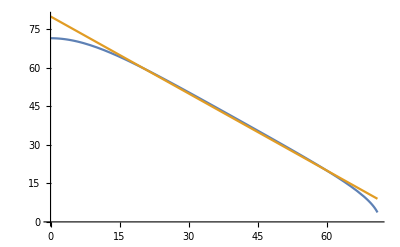

```mathematica
Plot[{a* 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.475, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> bscaled * Pi/180}}, 80 - bscaled}, {bscaled, 0, 71}]
```

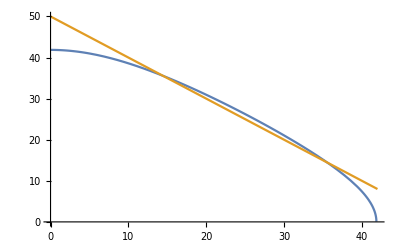

```mathematica
Plot[{a* 180 / Pi/.{DetermineOtherAngle /. {mintakeup -> 0.25, Larm -> 0.25, dap -> 0.2, dpdp -> 0.1542, b-> bscaled * Pi/180}}, 50 - bscaled}, {bscaled, 0, 42}]
```

```mathematica
yincline = Solve[{
Subscript[L, c]==  Sqrt[(X)^2 + Y^2]+ Sqrt[( Subscript[L, cs]-X)^2 + (Subscript[H, cs]-Y)^2]
}, {Y}, Reals][[1]]
```

{Y→ConditionalExpression[(-H_cs^3+H_cs L_c^2+2 X H_cs L_cs-H_cs L_cs^2)/(2 (-H_cs^2+L_c^2))-1/2 √((4 X^2 H_cs^2 L_c^2+H_cs^4 L_c^2-4 X^2 L_c^4-2 H_cs^2 L_c^4+L_c^6-4 X H_cs^2 L_c^2 L_cs+4 X L_c^4 L_cs+4 X^2 L_c^2 L_cs^2+2 H_cs^2 L_c^2 L_cs^2-2 L_c^4 L_cs^2-4 X L_c^2 L_cs^3+L_c^2 L_cs^4)/((-H_cs^2+L_c^2)^2)), ]}

```mathematica
Normal[Y/. {yincline /. {Subscript[H, cs]-> 30, Subscript[L, c] -> , Subscript[L, cs]-> 30}}]
```

{(21000+1800 X)/3200-(√(1225000000+210000000 X-7000000 X^2))/3200}

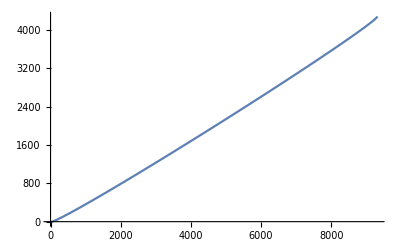

```mathematica
Plot[{Normal[Y/. {yincline /. {Subscript[H, cs]-> 4282 , Subscript[L, c] -> 10280, Subscript[L, cs]-> 9320}}]}, {X, 0, 9320}]
```

```mathematica
test = N[N[Table[Normal[Y/. {yincline /. {Subscript[H, cs]-> 4292 , Subscript[L, c] -> 10265, Subscript[L, cs]-> 9320}}],{X, 0, 9320, 5}]]]
```

{{-2.97317},{-4.63515},{-5.0286},{-4.90902},{-4.48991},{-3.86811},{-3.0973},{-2.21095},{-1.23158},{-0.175209},{0.946274},{2.12378},{3.35015},{4.61964},{5.92757},{7.27003},{8.64375},{10.046},{11.4742},{12.9265},{14.401},{15.8961},{17.4104},{18.9426},{20.4917},{22.0566},{23.6363},{25.2302},{26.8374},{28.4572},{30.089},{31.7323},{33.3864},{35.051},{36.7255},{38.4096},{40.1028},{41.8047},{43.5152},{45.2337},{46.96},{48.6938},{50.435},{52.1831},{53.938},{55.6995},{57.4673},{59.2413},{61.0212},{62.8069},{64.5982},{66.395},{68.1971},{70.0043},{71.8165},{73.6337},{75.4555},{77.282},{79.113},{80.9484},{82.7881},{84.632},{86.48},{88.3319},{90.1878},{92.0475},{93.9109},{95.778},{97.6487},{99.5229},{101.4},{103.281},{105.166},{107.053},{108.944},{110.837},{112.734},{114.634},{116.537},{118.442},{120.351},{122.262},{124.176},{126.092},{128.012},{129.933},{131.858},{133.785},{135.714},{137.646},{139.58},{141.516},{143.455},{145.396},{147.339},{149.285},{151.233},{153.182},{155.134},{157.088},{159.044},{161.003},{162.963},{164.925},{166.889},{168.855},{170.822},{172.792},{174.764},{176.737},{178.712},{180.689},{182.668},{184.648},{186.63},{188.614},{190.599},{192.586},{194.575},{196.565},{198.557},{200.55},{202.545},{204.542},{206.54},{208.54},{210.541},{212.543},{214.547},{216.552},{218.559},{220.567},{222.577},{224.588},{226.6},{228.614},{230.629},{232.645},{234.663},{236.682},{238.702},{240.723},{242.746},{244.77},{246.795},{248.821},{250.849},{252.878},{254.908},{256.939},{258.971},{261.005},{263.039},{265.075},{267.112},{269.15},{271.189},{273.229},{275.27},{277.313},{279.356},{281.4},{283.446},{285.492},{287.54},{289.589},{291.638},{293.689},{295.74},{297.793},{299.846},{301.901},{303.957},{306.013},{308.07},{310.129},{312.188},{314.248},{316.309},{318.371},{320.434},{322.498},{324.563},{326.629},{328.695},{330.763},{332.831},{334.9},{336.97},{339.041},{341.112},{343.185},{345.258},{347.332},{349.407},{351.483},{353.56},{355.637},{357.716},{359.795},{361.874},{363.955},{366.036},{368.119},{370.201},{372.285},{374.37},{376.455},{378.541},{380.627},{382.715},{384.803},{386.892},{388.981},{391.072},{393.163},{395.255},{397.347},{399.44},{401.534},{403.629},{405.724},{407.82},{409.917},{412.014},{414.112},{416.21},{418.31},{420.41},{422.51},{424.612},{426.714},{428.816},{430.92},{433.024},{435.128},{437.233},{439.339},{441.445},{443.553},{445.66},{447.769},{449.877},{451.987},{454.097},{456.208},{458.319},{460.431},{462.544},{464.657},{466.771},{468.885},{471.},{473.115},{475.231},{477.348},{479.465},{481.583},{483.701},{485.82},{487.94},{490.06},{492.18},{494.301},{496.423},{498.545},{500.668},{502.791},{504.915},{507.04},{509.165},{511.29},{513.416},{515.543},{517.67},{519.797},{521.925},{524.054},{526.183},{528.313},{530.443},{532.574},{534.705},{536.837},{538.969},{541.101},{543.235},{545.368},{547.503},{549.637},{551.772},{553.908},{556.044},{558.181},{560.318},{562.455},{564.594},{566.732},{568.871},{571.011},{573.151},{575.291},{577.432},{579.573},{581.715},{583.857},{586.},{588.143},{590.287},{592.431},{594.576},{596.721},{598.866},{601.012},{603.158},{605.305},{607.452},{609.6},{611.748},{613.897},{616.046},{618.195},{620.345},{622.495},{624.646},{626.797},{628.949},{631.101},{633.253},{635.406},{637.559},{639.713},{641.867},{644.021},{646.176},{648.332},{650.487},{652.644},{654.8},{656.957},{659.114},{661.272},{663.43},{665.589},{667.748},{669.907},{672.067},{674.227},{676.388},{678.549},{680.71},{682.872},{685.034},{687.197},{689.359},{691.523},{693.686},{695.85},{698.015},{700.18},{702.345},{704.511},{706.676},{708.843},{711.01},{713.177},{715.344},{717.512},{719.68},{721.849},{724.018},{726.187},{728.356},{730.526},{732.697},{734.868},{737.039},{739.21},{741.382},{743.554},{745.727},{747.9},{750.073},{752.247},{754.42},{756.595},{758.769},{760.944},{763.12},{765.296},{767.472},{769.648},{771.825},{774.002},{776.179},{778.357},{780.535},{782.714},{784.892},{787.072},{789.251},{791.431},{793.611},{795.791},{797.972},{800.153},{802.335},{804.517},{806.699},{808.881},{811.064},{813.247},{815.431},{817.614},{819.798},{821.983},{824.168},{826.353},{828.538},{830.724},{832.91},{835.096},{837.283},{839.47},{841.657},{843.845},{846.033},{848.221},{850.409},{852.598},{854.787},{856.977},{859.167},{861.357},{863.547},{865.738},{867.929},{870.12},{872.312},{874.504},{876.696},{878.889},{881.082},{883.275},{885.468},{887.662},{889.856},{892.05},{894.245},{896.44},{898.635},{900.831},{903.027},{905.223},{907.419},{909.616},{911.813},{914.011},{916.208},{918.406},{920.604},{922.803},{925.002},{927.201},{929.4},{931.6},{933.8},{936.},{938.2},{940.401},{942.602},{944.804},{947.005},{949.207},{951.409},{953.612},{955.815},{958.018},{960.221},{962.425},{964.629},{966.833},{969.037},{971.242},{973.447},{975.652},{977.858},{980.064},{982.27},{984.476},{986.683},{988.89},{991.097},{993.304},{995.512},{997.72},{999.928},{1002.14},{1004.35},{1006.55},{1008.76},{1010.97},{1013.18},{1015.39},{1017.6},{1019.81},{1022.03},{1024.24},{1026.45},{1028.66},{1030.87},{1033.08},{1035.3},{1037.51},{1039.72},{1041.94},{1044.15},{1046.36},{1048.58},{1050.79},{1053.01},{1055.22},{1057.44},{1059.65},{1061.87},{1064.08},{1066.3},{1068.52},{1070.73},{1072.95},{1075.17},{1077.38},{1079.6},{1081.82},{1084.04},{1086.26},{1088.48},{1090.69},{1092.91},{1095.13},{1097.35},{1099.57},{1101.79},{1104.01},{1106.23},{1108.45},{1110.68},{1112.9},{1115.12},{1117.34},{1119.56},{1121.79},{1124.01},{1126.23},{1128.45},{1130.68},{1132.9},{1135.13},{1137.35},{1139.57},{1141.8},{1144.02},{1146.25},{1148.47},{1150.7},{1152.93},{1155.15},{1157.38},{1159.6},{1161.83},{1164.06},{1166.28},{1168.51},{1170.74},{1172.97},{1175.2},{1177.42},{1179.65},{1181.88},{1184.11},{1186.34},{1188.57},{1190.8},{1193.03},{1195.26},{1197.49},{1199.72},{1201.95},{1204.18},{1206.42},{1208.65},{1210.88},{1213.11},{1215.34},{1217.58},{1219.81},{1222.04},{1224.28},{1226.51},{1228.74},{1230.98},{1233.21},{1235.45},{1237.68},{1239.92},{1242.15},{1244.39},{1246.62},{1248.86},{1251.09},{1253.33},{1255.57},{1257.8},{1260.04},{1262.28},{1264.51},{1266.75},{1268.99},{1271.23},{1273.47},{1275.7},{1277.94},{1280.18},{1282.42},{1284.66},{1286.9},{1289.14},{1291.38},{1293.62},{1295.86},{1298.1},{1300.34},{1302.58},{1304.83},{1307.07},{1309.31},{1311.55},{1313.79},{1316.04},{1318.28},{1320.52},{1322.76},{1325.01},{1327.25},{1329.49},{1331.74},{1333.98},{1336.23},{1338.47},{1340.72},{1342.96},{1345.21},{1347.45},{1349.7},{1351.94},{1354.19},{1356.44},{1358.68},{1360.93},{1363.18},{1365.42},{1367.67},{1369.92},{1372.17},{1374.42},{1376.66},{1378.91},{1381.16},{1383.41},{1385.66},{1387.91},{1390.16},{1392.41},{1394.66},{1396.91},{1399.16},{1401.41},{1403.66},{1405.91},{1408.16},{1410.41},{1412.66},{1414.92},{1417.17},{1419.42},{1421.67},{1423.93},{1426.18},{1428.43},{1430.69},{1432.94},{1435.19},{1437.45},{1439.7},{1441.96},{1444.21},{1446.46},{1448.72},{1450.97},{1453.23},{1455.49},{1457.74},{1460.},{1462.25},{1464.51},{1466.77},{1469.02},{1471.28},{1473.54},{1475.79},{1478.05},{1480.31},{1482.57},{1484.83},{1487.08},{1489.34},{1491.6},{1493.86},{1496.12},{1498.38},{1500.64},{1502.9},{1505.16},{1507.42},{1509.68},{1511.94},{1514.2},{1516.46},{1518.72},{1520.99},{1523.25},{1525.51},{1527.77},{1530.03},{1532.3},{1534.56},{1536.82},{1539.08},{1541.35},{1543.61},{1545.87},{1548.14},{1550.4},{1552.67},{1554.93},{1557.2},{1559.46},{1561.73},{1563.99},{1566.26},{1568.52},{1570.79},{1573.05},{1575.32},{1577.59},{1579.85},{1582.12},{1584.39},{1586.65},{1588.92},{1591.19},{1593.46},{1595.72},{1597.99},{1600.26},{1602.53},{1604.8},{1607.07},{1609.34},{1611.61},{1613.88},{1616.15},{1618.42},{1620.69},{1622.96},{1625.23},{1627.5},{1629.77},{1632.04},{1634.31},{1636.58},{1638.85},{1641.13},{1643.4},{1645.67},{1647.94},{1650.21},{1652.49},{1654.76},{1657.03},{1659.31},{1661.58},{1663.85},{1666.13},{1668.4},{1670.68},{1672.95},{1675.23},{1677.5},{1679.78},{1682.05},{1684.33},{1686.6},{1688.88},{1691.16},{1693.43},{1695.71},{1697.98},{1700.26},{1702.54},{1704.82},{1707.09},{1709.37},{1711.65},{1713.93},{1716.21},{1718.48},{1720.76},{1723.04},{1725.32},{1727.6},{1729.88},{1732.16},{1734.44},{1736.72},{1739.},{1741.28},{1743.56},{1745.84},{1748.12},{1750.4},{1752.68},{1754.96},{1757.25},{1759.53},{1761.81},{1764.09},{1766.37},{1768.66},{1770.94},{1773.22},{1775.51},{1777.79},{1780.07},{1782.36},{1784.64},{1786.92},{1789.21},{1791.49},{1793.78},{1796.06},{1798.35},{1800.63},{1802.92},{1805.2},{1807.49},{1809.78},{1812.06},{1814.35},{1816.63},{1818.92},{1821.21},{1823.5},{1825.78},{1828.07},{1830.36},{1832.65},{1834.93},{1837.22},{1839.51},{1841.8},{1844.09},{1846.38},{1848.67},{1850.96},{1853.25},{1855.54},{1857.82},{1860.12},{1862.41},{1864.7},{1866.99},{1869.28},{1871.57},{1873.86},{1876.15},{1878.44},{1880.73},{1883.03},{1885.32},{1887.61},{1889.9},{1892.2},{1894.49},{1896.78},{1899.08},{1901.37},{1903.66},{1905.96},{1908.25},{1910.54},{1912.84},{1915.13},{1917.43},{1919.72},{1922.02},{1924.31},{1926.61},{1928.91},{1931.2},{1933.5},{1935.79},{1938.09},{1940.39},{1942.68},{1944.98},{1947.28},{1949.58},{1951.87},{1954.17},{1956.47},{1958.77},{1961.07},{1963.36},{1965.66},{1967.96},{1970.26},{1972.56},{1974.86},{1977.16},{1979.46},{1981.76},{1984.06},{1986.36},{1988.66},{1990.96},{1993.26},{1995.56},{1997.86},{2000.17},{2002.47},{2004.77},{2007.07},{2009.37},{2011.68},{2013.98},{2016.28},{2018.58},{2020.89},{2023.19},{2025.49},{2027.8},{2030.1},{2032.41},{2034.71},{2037.01},{2039.32},{2041.62},{2043.93},{2046.23},{2048.54},{2050.85},{2053.15},{2055.46},{2057.76},{2060.07},{2062.38},{2064.68},{2066.99},{2069.3},{2071.6},{2073.91},{2076.22},{2078.53},{2080.83},{2083.14},{2085.45},{2087.76},{2090.07},{2092.38},{2094.69},{2097.},{2099.31},{2101.62},{2103.93},{2106.24},{2108.55},{2110.86},{2113.17},{2115.48},{2117.79},{2120.1},{2122.41},{2124.72},{2127.03},{2129.35},{2131.66},{2133.97},{2136.28},{2138.6},{2140.91},{2143.22},{2145.54},{2147.85},{2150.16},{2152.48},{2154.79},{2157.1},{2159.42},{2161.73},{2164.05},{2166.36},{2168.68},{2170.99},{2173.31},{2175.62},{2177.94},{2180.26},{2182.57},{2184.89},{2187.21},{2189.52},{2191.84},{2194.16},{2196.47},{2198.79},{2201.11},{2203.43},{2205.75},{2208.06},{2210.38},{2212.7},{2215.02},{2217.34},{2219.66},{2221.98},{2224.3},{2226.62},{2228.94},{2231.26},{2233.58},{2235.9},{2238.22},{2240.54},{2242.86},{2245.18},{2247.51},{2249.83},{2252.15},{2254.47},{2256.79},{2259.12},{2261.44},{2263.76},{2266.09},{2268.41},{2270.73},{2273.06},{2275.38},{2277.7},{2280.03},{2282.35},{2284.68},{2287.},{2289.33},{2291.65},{2293.98},{2296.3},{2298.63},{2300.95},{2303.28},{2305.61},{2307.93},{2310.26},{2312.59},{2314.91},{2317.24},{2319.57},{2321.9},{2324.23},{2326.55},{2328.88},{2331.21},{2333.54},{2335.87},{2338.2},{2340.53},{2342.86},{2345.19},{2347.51},{2349.84},{2352.18},{2354.51},{2356.84},{2359.17},{2361.5},{2363.83},{2366.16},{2368.49},{2370.82},{2373.16},{2375.49},{2377.82},{2380.15},{2382.49},{2384.82},{2387.15},{2389.49},{2391.82},{2394.15},{2396.49},{2398.82},{2401.16},{2403.49},{2405.82},{2408.16},{2410.49},{2412.83},{2415.17},{2417.5},{2419.84},{2422.17},{2424.51},{2426.85},{2429.18},{2431.52},{2433.86},{2436.19},{2438.53},{2440.87},{2443.21},{2445.55},{2447.88},{2450.22},{2452.56},{2454.9},{2457.24},{2459.58},{2461.92},{2464.26},{2466.6},{2468.94},{2471.28},{2473.62},{2475.96},{2478.3},{2480.64},{2482.98},{2485.32},{2487.67},{2490.01},{2492.35},{2494.69},{2497.04},{2499.38},{2501.72},{2504.06},{2506.41},{2508.75},{2511.09},{2513.44},{2515.78},{2518.13},{2520.47},{2522.82},{2525.16},{2527.51},{2529.85},{2532.2},{2534.54},{2536.89},{2539.24},{2541.58},{2543.93},{2546.28},{2548.62},{2550.97},{2553.32},{2555.67},{2558.01},{2560.36},{2562.71},{2565.06},{2567.41},{2569.76},{2572.1},{2574.45},{2576.8},{2579.15},{2581.5},{2583.85},{2586.2},{2588.55},{2590.91},{2593.26},{2595.61},{2597.96},{2600.31},{2602.66},{2605.01},{2607.37},{2609.72},{2612.07},{2614.43},{2616.78},{2619.13},{2621.49},{2623.84},{2626.19},{2628.55},{2630.9},{2633.26},{2635.61},{2637.97},{2640.32},{2642.68},{2645.03},{2647.39},{2649.74},{2652.1},{2654.46},{2656.81},{2659.17},{2661.53},{2663.89},{2666.24},{2668.6},{2670.96},{2673.32},{2675.68},{2678.04},{2680.39},{2682.75},{2685.11},{2687.47},{2689.83},{2692.19},{2694.55},{2696.91},{2699.27},{2701.63},{2704.},{2706.36},{2708.72},{2711.08},{2713.44},{2715.81},{2718.17},{2720.53},{2722.89},{2725.26},{2727.62},{2729.98},{2732.35},{2734.71},{2737.08},{2739.44},{2741.81},{2744.17},{2746.54},{2748.9},{2751.27},{2753.63},{2756.},{2758.36},{2760.73},{2763.1},{2765.47},{2767.83},{2770.2},{2772.57},{2774.94},{2777.3},{2779.67},{2782.04},{2784.41},{2786.78},{2789.15},{2791.52},{2793.89},{2796.26},{2798.63},{2801.},{2803.37},{2805.74},{2808.11},{2810.48},{2812.85},{2815.23},{2817.6},{2819.97},{2822.34},{2824.72},{2827.09},{2829.46},{2831.84},{2834.21},{2836.58},{2838.96},{2841.33},{2843.71},{2846.08},{2848.46},{2850.83},{2853.21},{2855.58},{2857.96},{2860.34},{2862.71},{2865.09},{2867.47},{2869.85},{2872.22},{2874.6},{2876.98},{2879.36},{2881.74},{2884.12},{2886.49},{2888.87},{2891.25},{2893.63},{2896.01},{2898.39},{2900.77},{2903.16},{2905.54},{2907.92},{2910.3},{2912.68},{2915.06},{2917.45},{2919.83},{2922.21},{2924.59},{2926.98},{2929.36},{2931.75},{2934.13},{2936.51},{2938.9},{2941.28},{2943.67},{2946.05},{2948.44},{2950.83},{2953.21},{2955.6},{2957.99},{2960.37},{2962.76},{2965.15},{2967.53},{2969.92},{2972.31},{2974.7},{2977.09},{2979.48},{2981.87},{2984.26},{2986.65},{2989.04},{2991.43},{2993.82},{2996.21},{2998.6},{3000.99},{3003.38},{3005.77},{3008.17},{3010.56},{3012.95},{3015.35},{3017.74},{3020.13},{3022.53},{3024.92},{3027.32},{3029.71},{3032.1},{3034.5},{3036.9},{3039.29},{3041.69},{3044.08},{3046.48},{3048.88},{3051.28},{3053.67},{3056.07},{3058.47},{3060.87},{3063.27},{3065.66},{3068.06},{3070.46},{3072.86},{3075.26},{3077.66},{3080.06},{3082.46},{3084.87},{3087.27},{3089.67},{3092.07},{3094.47},{3096.88},{3099.28},{3101.68},{3104.09},{3106.49},{3108.89},{3111.3},{3113.7},{3116.11},{3118.51},{3120.92},{3123.32},{3125.73},{3128.14},{3130.54},{3132.95},{3135.36},{3137.77},{3140.17},{3142.58},{3144.99},{3147.4},{3149.81},{3152.22},{3154.63},{3157.04},{3159.45},{3161.86},{3164.27},{3166.68},{3169.09},{3171.51},{3173.92},{3176.33},{3178.74},{3181.16},{3183.57},{3185.99},{3188.4},{3190.81},{3193.23},{3195.64},{3198.06},{3200.48},{3202.89},{3205.31},{3207.72},{3210.14},{3212.56},{3214.98},{3217.4},{3219.81},{3222.23},{3224.65},{3227.07},{3229.49},{3231.91},{3234.33},{3236.75},{3239.17},{3241.59},{3244.02},{3246.44},{3248.86},{3251.28},{3253.71},{3256.13},{3258.55},{3260.98},{3263.4},{3265.83},{3268.25},{3270.68},{3273.1},{3275.53},{3277.96},{3280.38},{3282.81},{3285.24},{3287.67},{3290.1},{3292.52},{3294.95},{3297.38},{3299.81},{3302.24},{3304.67},{3307.1},{3309.54},{3311.97},{3314.4},{3316.83},{3319.26},{3321.7},{3324.13},{3326.56},{3329.},{3331.43},{3333.87},{3336.3},{3338.74},{3341.18},{3343.61},{3346.05},{3348.49},{3350.92},{3353.36},{3355.8},{3358.24},{3360.68},{3363.12},{3365.56},{3368.},{3370.44},{3372.88},{3375.32},{3377.76},{3380.21},{3382.65},{3385.09},{3387.54},{3389.98},{3392.42},{3394.87},{3397.31},{3399.76},{3402.21},{3404.65},{3407.1},{3409.55},{3411.99},{3414.44},{3416.89},{3419.34},{3421.79},{3424.24},{3426.69},{3429.14},{3431.59},{3434.04},{3436.5},{3438.95},{3441.4},{3443.85},{3446.31},{3448.76},{3451.22},{3453.67},{3456.13},{3458.58},{3461.04},{3463.5},{3465.95},{3468.41},{3470.87},{3473.33},{3475.79},{3478.25},{3480.71},{3483.17},{3485.63},{3488.09},{3490.55},{3493.02},{3495.48},{3497.94},{3500.41},{3502.87},{3505.34},{3507.8},{3510.27},{3512.73},{3515.2},{3517.67},{3520.14},{3522.6},{3525.07},{3527.54},{3530.01},{3532.48},{3534.95},{3537.42},{3539.9},{3542.37},{3544.84},{3547.32},{3549.79},{3552.26},{3554.74},{3557.21},{3559.69},{3562.17},{3564.64},{3567.12},{3569.6},{3572.08},{3574.56},{3577.04},{3579.52},{3582.},{3584.48},{3586.96},{3589.45},{3591.93},{3594.41},{3596.9},{3599.38},{3601.87},{3604.36},{3606.84},{3609.33},{3611.82},{3614.31},{3616.8},{3619.29},{3621.78},{3624.27},{3626.76},{3629.25},{3631.74},{3634.24},{3636.73},{3639.23},{3641.72},{3644.22},{3646.71},{3649.21},{3651.71},{3654.21},{3656.71},{3659.21},{3661.71},{3664.21},{3666.71},{3669.21},{3671.72},{3674.22},{3676.73},{3679.23},{3681.74},{3684.24},{3686.75},{3689.26},{3691.77},{3694.28},{3696.79},{3699.3},{3701.81},{3704.32},{3706.84},{3709.35},{3711.86},{3714.38},{3716.9},{3719.41},{3721.93},{3724.45},{3726.97},{3729.49},{3732.01},{3734.53},{3737.05},{3739.58},{3742.1},{3744.62},{3747.15},{3749.68},{3752.2},{3754.73},{3757.26},{3759.79},{3762.32},{3764.85},{3767.39},{3769.92},{3772.45},{3774.99},{3777.52},{3780.06},{3782.6},{3785.14},{3787.68},{3790.22},{3792.76},{3795.3},{3797.84},{3800.39},{3802.93},{3805.48},{3808.02},{3810.57},{3813.12},{3815.67},{3818.22},{3820.77},{3823.33},{3825.88},{3828.44},{3830.99},{3833.55},{3836.11},{3838.67},{3841.23},{3843.79},{3846.35},{3848.92},{3851.48},{3854.05},{3856.61},{3859.18},{3861.75},{3864.32},{3866.89},{3869.47},{3872.04},{3874.62},{3877.19},{3879.77},{3882.35},{3884.93},{3887.51},{3890.09},{3892.68},{3895.26},{3897.85},{3900.44},{3903.03},{3905.62},{3908.21},{3910.81},{3913.4},{3916.},{3918.6},{3921.2},{3923.8},{3926.4},{3929.},{3931.61},{3934.22},{3936.82},{3939.44},{3942.05},{3944.66},{3947.28},{3949.89},{3952.51},{3955.13},{3957.75},{3960.38},{3963.},{3965.63},{3968.26},{3970.89},{3973.52},{3976.16},{3978.79},{3981.43},{3984.07},{3986.71},{3989.36},{3992.01},{3994.65},{3997.31},{3999.96},{4002.61},{4005.27},{4007.93},{4010.59},{4013.26},{4015.92},{4018.59},{4021.26},{4023.94},{4026.61},{4029.29},{4031.97},{4034.66},{4037.34},{4040.03},{4042.72},{4045.42},{4048.12},{4050.82},{4053.52},{4056.23},{4058.94},{4061.65},{4064.37},{4067.09},{4069.81},{4072.54},{4075.27},{4078.},{4080.74},{4083.48},{4086.22},{4088.97},{4091.72},{4094.48},{4097.24},{4100.01},{4102.78},{4105.55},{4108.33},{4111.11},{4113.9},{4116.69},{4119.49},{4122.3},{4125.11},{4127.92},{4130.74},{4133.57},{4136.4},{4139.24},{4142.09},{4144.94},{4147.8},{4150.66},{4153.54},{4156.42},{4159.31},{4162.21},{4165.12},{4168.03},{4170.96},{4173.9},{4176.84},{4179.8},{4182.77},{4185.75},{4188.74},{4191.75},{4194.77},{4197.81},{4200.86},{4203.93},{4207.01},{4210.12},{4213.24},{4216.39},{4219.56},{4222.76},{4225.99},{4229.25},{4232.54},{4235.87},{4239.24},{4242.67},{4246.15},{4249.69},{4253.31},{4257.03},{4260.86},{4264.83},{4269.02},{4273.5},{4278.49},{4284.75}}

```mathematica
Export["bad.xls",test, "XLS"]
```

bad.xls

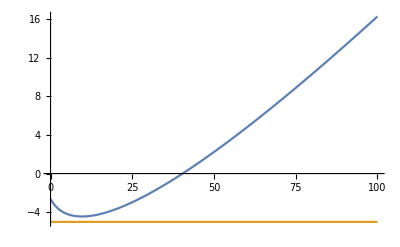

```mathematica
Plot[{Normal[Y/. {yincline /. {Subscript[H, cs]-> 4272 , Subscript[L, c] -> 10264.5, Subscript[L, cs]-> 9320}}], {X = -5.0}}, {X, 0, 100}]
```

```mathematica
D[Normal[Y/. {yincline }], X]
```

{(H_cs L_cs)/(-H_cs^2+L_c^2)-(8 X H_cs^2 L_c^2-8 X L_c^4-4 H_cs^2 L_c^2 L_cs+4 L_c^4 L_cs+8 X L_c^2 L_cs^2-4 L_c^2 L_cs^3)/(4 (-H_cs^2+L_c^2)^2 √((4 X^2 H_cs^2 L_c^2+H_cs^4 L_c^2-4 X^2 L_c^4-2 H_cs^2 L_c^4+L_c^6-4 X H_cs^2 L_c^2 L_cs+4 X L_c^4 L_cs+4 X^2 L_c^2 L_cs^2+2 H_cs^2 L_c^2 L_cs^2-2 L_c^4 L_cs^2-4 X L_c^2 L_cs^3+L_c^2 L_cs^4)/((-H_cs^2+L_c^2)^2)))}

```mathematica
(Subscript[H, cs] Subscript[L, cs])/(-Subscript[H, cs]^2+Subscript[L, c]^2)-(8 X Subscript[H, cs]^2 Subscript[L, c]^2-8 X Subscript[L, c]^4-4 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]+4 Subscript[L, c]^4 Subscript[L, cs]+8 X Subscript[L, c]^2 Subscript[L, cs]^2-4 Subscript[L, c]^2 Subscript[L, cs]^3)/(4 (-Subscript[H, cs]^2+Subscript[L, c]^2)^2 √((4 X^2 Subscript[H, cs]^2 Subscript[L, c]^2+Subscript[H, cs]^4 Subscript[L, c]^2-4 X^2 Subscript[L, c]^4-2 Subscript[H, cs]^2 Subscript[L, c]^4+Subscript[L, c]^6-4 X Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]+4 X Subscript[L, c]^4 Subscript[L, cs]+4 X^2 Subscript[L, c]^2 Subscript[L, cs]^2+2 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]^2-2 Subscript[L, c]^4 Subscript[L, cs]^2-4 X Subscript[L, c]^2 Subscript[L, cs]^3+Subscript[L, c]^2 Subscript[L, cs]^4)/((-Subscript[H, cs]^2+Subscript[L, c]^2)^2)))/. {Subscript[H, cs]-> H, Subscript[L, c]-> LC, Subscript[L, cs]-> CS }
```

(CS H)/(-H^2+LC^2)-(-4 CS^3 LC^2-4 CS H^2 LC^2+4 CS LC^4+8 CS^2 LC^2 X+8 H^2 LC^2 X-8 LC^4 X)/(4 (-H^2+LC^2)^2 √((CS^4 LC^2+2 CS^2 H^2 LC^2+H^4 LC^2-2 CS^2 LC^4-2 H^2 LC^4+LC^6-4 CS^3 LC^2 X-4 CS H^2 LC^2 X+4 CS LC^4 X+4 CS^2 LC^2 X^2+4 H^2 LC^2 X^2-4 LC^4 X^2)/((-H^2+LC^2)^2)))

```mathematica
Manipulate[Plot[Abs[(CS H)/(-H^2+LC^2)-(-4 CS^3 LC^2-4 CS H^2 LC^2+4 CS LC^4+8 CS^2 LC^2 X+8 H^2 LC^2 X-8 LC^4 X)/(4 (-H^2+LC^2)^2 √((CS^4 LC^2+2 CS^2 H^2 LC^2+H^4 LC^2-2 CS^2 LC^4-2 H^2 LC^4+LC^6-4 CS^3 LC^2 X-4 CS H^2 LC^2 X+4 CS LC^4 X+4 CS^2 LC^2 X^2+4 H^2 LC^2 X^2-4 LC^4 X^2)/((-H^2+LC^2)^2)))],{X, 0, LC}], {LC,0.1, 1}, {CS ,0.1, 20}]
```

```mathematica
Solve[FullSimplify[(Subscript[H, cs] Subscript[L, cs])/(-Subscript[H, cs]^2+Subscript[L, c]^2)-(-4 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]+4 Subscript[L, c]^4 Subscript[L, cs]-4 Subscript[L, c]^2 Subscript[L, cs]^3)/(4 (-Subscript[H, cs]^2+Subscript[L, c]^2)^2 √((Subscript[H, cs]^4 Subscript[L, c]^2-2 Subscript[H, cs]^2 Subscript[L, c]^4+Subscript[L, c]^6+2 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]^2-2 Subscript[L, c]^4 Subscript[L, cs]^2+Subscript[L, c]^2 Subscript[L, cs]^4)/((-Subscript[H, cs]^2+Subscript[L, c]^2)^2))) == 0], Subscript[L, c], Reals]
```

{}

```mathematica
FullSimplify[(Subscript[H, cs] Subscript[L, cs])/(-Subscript[H, cs]^2+Subscript[L, c]^2)-(-4 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]+4 Subscript[L, c]^4 Subscript[L, cs]-4 Subscript[L, c]^2 Subscript[L, cs]^3)/(4 (-Subscript[H, cs]^2+Subscript[L, c]^2)^2 √((Subscript[H, cs]^4 Subscript[L, c]^2-2 Subscript[H, cs]^2 Subscript[L, c]^4+Subscript[L, c]^6+2 Subscript[H, cs]^2 Subscript[L, c]^2 Subscript[L, cs]^2-2 Subscript[L, c]^4 Subscript[L, cs]^2+Subscript[L, c]^2 Subscript[L, cs]^4)/((-Subscript[H, cs]^2+Subscript[L, c]^2)^2))), Reals]
```

(L_cs (H_cs (-H_cs^2+L_c^2)+(L_c^2 (H_cs^2-L_c^2+L_cs^2))/(√((L_c^2 (H_cs^2-L_c^2+L_cs^2)^2)/((H_cs^2-L_c^2)^2)))))/((H_cs^2-L_c^2)^2)

```mathematica
Solve[Subscript[L, cs] (Subscript[H, cs] (-Subscript[H, cs]^2+Subscript[L, c]^2)+(Subscript[L, c]^2 (Subscript[H, cs]^2-Subscript[L, c]^2+Subscript[L, cs]^2))/(√((Subscript[L, c]^2 (Subscript[H, cs]^2-Subscript[L, c]^2+Subscript[L, cs]^2)^2)/((Subscript[H, cs]^2-Subscript[L, c]^2)^2)))) == 0, Subscript[L, c]]
```

```mathematica
(CS H)/(-H^2+LC^2)-(-4 CS^3 LC^2-4 CS H^2 LC^2+4 CS LC^4+8 CS^2 LC^2 X+8 H^2 LC^2 X-8 LC^4 X)/(4 (-H^2+LC^2)^2 √((CS^4 LC^2+2 CS^2 H^2 LC^2+H^4 LC^2-2 CS^2 LC^4-2 H^2 LC^4+LC^6-4 CS^3 LC^2 X-4 CS H^2 LC^2 X+4 CS LC^4 X+4 CS^2 LC^2 X^2+4 H^2 LC^2 X^2-4 LC^4 X^2)/((-H^2+LC^2)^2))) /. {X-> 0}
```

(CS H)/(-H^2+LC^2)-(-4 CS^3 LC^2-4 CS H^2 LC^2+4 CS LC^4)/(4 (-H^2+LC^2)^2 √((CS^4 LC^2+2 CS^2 H^2 LC^2+H^4 LC^2-2 CS^2 LC^4-2 H^2 LC^4+LC^6)/((-H^2+LC^2)^2)))

```mathematica
Solve[(CS H)/(-H^2+LC^2)-(-4 CS^3 LC^2-4 CS H^2 LC^2+4 CS LC^4+8 CS^2 LC^2 X+8 H^2 LC^2 X-8 LC^4 X)/(4 (-H^2+LC^2)^2 √((CS^4 LC^2+2 CS^2 H^2 LC^2+H^4 LC^2-2 CS^2 LC^4-2 H^2 LC^4+LC^6-4 CS^3 LC^2 X-4 CS H^2 LC^2 X+4 CS LC^4 X+4 CS^2 LC^2 X^2+4 H^2 LC^2 X^2-4 LC^4 X^2)/((-H^2+LC^2)^2)))==0, X, Reals]
```

{{X→ConditionalExpression[CS/2-1/2 √(-(CS^2 H^2)/(CS^2-LC^2)), ]},{X→ConditionalExpression[CS/2+1/2 √(-(CS^2 H^2)/(CS^2-LC^2)), ]}}

```mathematica
FullSimplify[yincline/.{X->CS/2-1/2 √(-(CS^2 H^2)/(CS^2-LC^2))/.{CS-> Subscript[L, cs], H -> Subscript[H, cs], LC -> Subscript[L, c]}}]
```

{Y→ConditionalExpression[(-L_c^4-Abs[H_cs] Abs[L_cs] H_cs L_cs-H_cs^3 √(L_c^2-L_cs^2)+H_cs L_c^2 √(L_c^2-L_cs^2)+L_c^2 (H_cs^2+L_cs^2))/(2 (-H_cs^2+L_c^2) √(L_c^2-L_cs^2)), ]}

```mathematica
√((CS^4+CS^2 H^2-4 CS^3 X+4 CS^2 X^2)/(CS-2 X)^2)/. {X-> 0}
```

```mathematica
Sqrt[(H-√((CS^4+CS^2 H^2-4 CS^3 X+4 CS^2 X^2)/(CS-2 X)^2))]
```

```mathematica
FullSimplify[√((CS^4+CS^2 H^2)/CS^2)]
```

√(CS^2+H^2)

```mathematica
xysoln
```

{}